# Invariantes de curvas elípticas

## Ecuaciones de Weierstrass

Primero definimos los coeficientes de una ecuación general de Weierstrass:

```mathematica
X015={1,1,1,-10,-10};
isogX015={1,1,1,0,0};
E50={1,0,1,-1,-2};
F50={1,0,1,-126,-552};
G50={1,0,1,-76,298};
H50={1,0,1,549,-2202};
```

Los coeficientes de Weiestrass de una curva de Frey asociada a la terna A+B+C=0 son

```mathematica
frey[A_,B_,C_]:={0,B-A,0,-A B,0}
```

```mathematica
Expand[x(x-A)(x+B)]
```

-A B x-A x^2+B x^2+x^3

Luego definimos la ecuación de Weierstrass con coeficientes ordenados (a_1,a_2,a_3,a_4,a_6) con variables (x,y):

```mathematica
F[a_,x_,y_]:=y^2+a[[1]] x y+a[[3]] y-(x^3+a[[2]] x^2+a[[4]] x+a[[5]])
```

Hacemos el cambio de variable y→1/2(y-a_1 x-a_3) para obtener  una ecuación de Weierstrass (semi) simplificada:

```mathematica
G[a_,x_,y_]:=Expand[4F[a,x,1/2(y-a[[1]] x-a[[3]])]]
```

Para simplificar más la ecuación, hacemos los cambios de variable x→(x-3 a_1^2-12 a_2), y→1/108 y para obtener  la ecuación de Weierstrass simplificada:

```mathematica
H[a_,x_,y_]:=Expand[108^2×G[a,(x-3(a[[1]]^2+4a[[2]]))/36,y/108]]
```

Por ejemplo para X_0(15)

```mathematica
{F[X015,x,y],G[X015,x,y],H[X015,x,y]}
```

{10+10 x-x^2-x^3+y+x y+y^2,39+38 x-5 x^2-4 x^3+y^2,263466+12987 x-x^3+y^2}

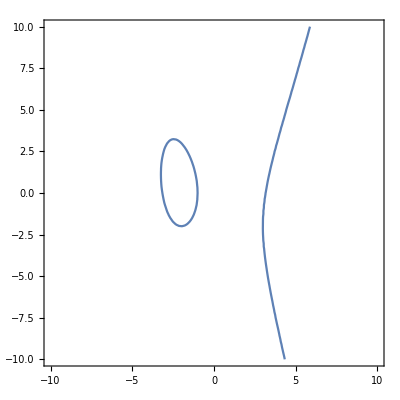

```mathematica
ContourPlot[F[X015,x,y]==0,{x,-10,10},{y,-10,10}]
```

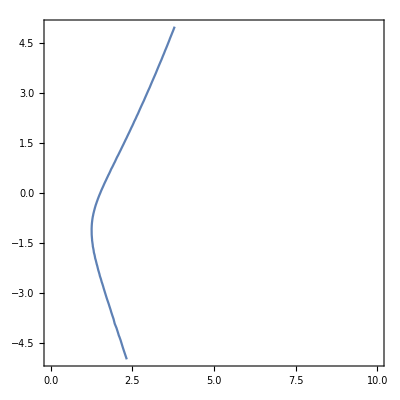

```mathematica
ContourPlot[F[E50,x,y]==0,{x,0,10},{y,-5,5}]
```

## Invariantes

Los invariantes de una curva con coeficientes “a” son:

```mathematica
b2[a_]:=a[[1]]^2+4*a[[2]]
b4[a_]:=2a[[4]]+a[[1]]a[[3]]
b6[a_]:=a[[3]]^3+4a[[5]]
b8[a_]:=a[[1]]^2a[[5]]+4a[[2]]a[[5]]-a[[1]]a[[3]]a[[4]]+a[[2]]a[[3]]^2-a[[4]]^2
c4[a_]:=b2[a]^2-24b4[a]
c6[a_]:=-b2[a]^3+36b2[a]b4[a]-216b6[a]
Δ[a_]:=-b2[a]^2 b8[a]-8b4[a]^3-27b6[a]^2+9b2[a]b4[a]b6[a]
j[a_]:=c4[a]^3/Δ[a]
```

```mathematica
{j[E50],j[F50],j[G50],j[H50]}
```

{-25/2,-349938025/8,-121945/32,46969655/32768}

```mathematica
MatrixForm[FactorInteger[{j[E50],j[F50],j[G50],j[H50]}]]
```

({{-1,1},{2,-1},{5,2}}
{{-1,1},{2,-3},{5,2},{241,3}}
{{-1,1},{2,-5},{5,1},{29,3}}
{{2,-15},{5,1},{211,3}})

```mathematica
Factor[Δ[frey[a,b,c]]]
```

16 a^2 b^2 (a+b)^2

## Reducción módulo p

Primero definimos una función que nos dice si los coeficientes de Weierstrass “a” determinan una curva no-singular (i.e. Δ≠0) y si es singular nos dice si tiene un nodo (i.e. Δ=0 y c_4≠0) o una cúspide (i.e.  Δ=0 y c_4=0):

```mathematica
suavidad[a_]:=If[!Δ[a]==0,"es no-singular",If[c4[a]==0,"tiene un nodo","tiene una cúspide"]]
```

```mathematica
suavidad[X015]
```

es no-singular

Similarmente definimos una función si nos dice si cierta curva con coeficientes de Weierstrass “a” tiene reducción buena o mala módulo un primo p y si tiene mala reducción nos dice el tipo de reducción (i.e. multiplicativa o aditiva):

```mathematica
redmodp[a_,p_]:=If[!Mod[Δ[a],p]==0,{"tiene buena reducción módulo"p},If[Mod[c4[a],p]==0,{"tiene reducción aditiva módulo "p},{"tiene reducción multiplicativa módulo "p}]]
```

```mathematica
F[frey[2,3,-5],x,y]
```

6 x-x^2-x^3+y^2

```mathematica
redmodp[frey[2,3,-5],2]
```

{2 tiene reducción aditiva módulo }

Con esto podemos calcular el conductor de una curva elíptica dada por unos coeficientes “a”. Primero definimos un exponente que codifica la información de la reducción módulo p (para característica ≠2,3):

```mathematica
redexp[a_,p_]:=If[!Mod[Δ[a],p]==0,0,If[Mod[c4[a],p]==0,2,1]]
```

```mathematica
redexp[frey[2,3,-5],2]
```

2

```mathematica
cond[a_]:=Product[p^(redexp[a,p]),{p,Select[Divisors[Δ[a]],PrimeQ]}]
```

```mathematica
cond[X015]
```

15

```mathematica
cond[E50]
```

50

```mathematica
cond[frey[a,b,c]]
```

∏_p^Divisors[] p^If[Mod[64 a^3 b^3+16 a^2 b^2 (-a+b)^2,p]≠0,0,If[Mod[c4[{0,-a+b,0,-a b,0}],p]==0,2,1]]

## Suma de E

Para calcular la suma de dos puntos P_1=(x_1,y_1) y P_2=(x_2,y_2), primero definimos las contantes λ y μ asociadas a dos puntos:

```mathematica
λ[a_,u_,v_]:=If[u[[1]]==v[[1]],(3 u[[1]]^2+2a[[2]]*u[[1]]+a[[4]]-a[[1]]*u[[2]])/(2 u[[2]]+a[[1]]*u[[1]]+a[[3]]),(v[[2]]-u[[2]])/(v[[1]]-u[[1]])]
μ[a_,u_,v_]:=If[u[[1]]==v[[1]],(-u[[1]]^3+a[[4]]*u[[1]]+2a[[5]]-a[[3]]*u[[2]])/(2 u[[2]]+a[[1]]*u[[1]]+a[[3]]),(u[[2]]*v[[1]]-u[[1]]*v[[2]])/(v[[1]]-u[[1]])]
```

La suma P_1+P_2 tiene coordenadas:

```mathematica
sumax[a_,u_,v_]:=(λ[a,u,v])^2+a[[1]]*λ[a,u,v]-a[[2]]-u[[1]]-v[[1]]
sumay[a_,u_,v_]:=-(λ[a,u,v]+a[[1]])*sumax[a,u,v]-μ[a,u,v]-a[[3]]
suma[a_,u_,v_]:=If[u[[1]]==v[[1]]&&u[[2]]+v[[2]]+a[[1]]*v[[1]]+a[[3]]==0,"O",{sumax[a,u,v],sumay[a,u,v]}]
```

Por ejemplo, sobre X_0(15), tenemos (-1,0)+(8,18)=

```mathematica
suma[X015,{-1,0},{8,18}]
```

{-2,3}

## Puntos de Torsión

Aquí usamos el teorema de Lutz-Nagell para encontrar los puntos de torsión de curvas elípticas cuyas ecuaciones simplificadas de Weierstrass tienen coeficientes enteros. Primero vemos qué puntos son de orden 2, i.e. los puntos (x,y) donde y=0. Los enlistamos con la función “tor2” que toma como argumento una lista de coeficientes de Weierstrass “a”:

```mathematica
tor2[a_]:=Table[{x,0},{x,Map[Last,Flatten[Solve[H[a,x,0]==0,x,Integers]/.Rule->List,1]]}]
```

```mathematica
tor2[X015]
```

{{-102,0},{-21,0},{123,0}}

```mathematica
tor2[isogX015]
```

{{-21,0}}

Después buscamos soluciones a la ecuación de Weierstrass con y^2|D donde D es la constante

```mathematica
d[a_]:=4*(-D[H[a,x,0],x]/. x->0)^3+27(H[a,0,0])^2
```

```mathematica
d[X015]
```

-6887475360000

```mathematica
FactorInteger[d[X015]]
```

{{-1,1},{2,8},{3,16},{5,4}}

Tomamos todos los divisores, positivos y negativos, cuyos cuadrados dividen a la constante D asociada a la ecuación con coeficientes “a”:

```mathematica
divcuad[a_]:=Select[Union[Divisors[d[a]],-Divisors[d[a]]],Divisible[d[a],#^2]&]
```

Para cada tal divisor y_0, resolvemos la ecuación de Weierstrass para encontrar coordenadas x asociadas a y_0. Juntamos estas soluciones al conjunto de torsion 2 y obtenemos todos los elementos no triviales del grupo de torsión de la curva con coeficientes “a”

```mathematica
tor[a_]:=Table[
{Last[Flatten[Solve[H[a,x,k]==0,x,Integers]/.Rule->List]],k},
{k,Select[divcuad[a],Length[Solve[H[a,x,#]==0,x,Integers]]>0&]}
]∪tor2[a]
```

```mathematica
tor[X015]
```

{{-102,0},{-57,-540},{-57,540},{-21,0},{123,0},{303,-4860},{303,4860}}

```mathematica
tor[E50]
```

{{75,-540},{75,540}}

## Isogenias

Aplicamos las ecuaciones de Vélu a una curva elíptica E y un subgrupo C de orden 2 generado por un punto P_0:

```mathematica
P0={-1,0};
X[a_,p_]:=p[[1]]+sumax[a,p,P0]-P0[[1]]
Y[a_,p_]:=p[[2]]+sumay[a,p,P0]-P0[[2]]
```

## Rango

Definimos ecuaciones de la forma y^2=x^3+a x^2+b x:

```mathematica
R[{a_,b_},x_,y_]:=y^2-(x^3+a x^2+b x)
```

```mathematica
R[{-63,1296},x,y]
```

-1296 x+63 x^2-x^3+y^2

Definimos div(b) como el conjunto de divisores positivos y negativos de b.

```mathematica
div[b_]:=Union[Divisors[b],-Divisors[b]]
```

Como solamente necesitamos el conjunto de divisores módulo ℚ^(*2), eliminamos la parte cuadrática de la factorización de los divisores con la función “librecuad” :

```mathematica
librecuad[δ_]:=δ*Max[Select[div[δ],Divisible[δ,#^2]&]]^-2
```

Aplicamos esta función al conjunto de divisores de b para obtener las clases módulo ℚ^(*2) de los divisores de b:

```mathematica
divmod[b_]:=Union[Map[librecuad,div[b]]]
```

```mathematica
{div[16],divmod[16]}
```

{{-16,-8,-4,-2,-1,1,2,4,8,16},{-2,-1,1,2}}

Para cada divisor δ de b definimos el polinomio homogéneo F_δ que define a la ecuación diofantina x^2=F_δ(Y,Z):

```mathematica
Fδ[δ_,{a_,b_},y_,z_]:=δ y^4+a y^2 z^2+b/δ z^4
```

Dado un divisor δ definimos la siguiente función para verificar si x^2=F_δ(Y,Z) tiene una solución en una lista “li” de ternas (X_0,Y_0,Z_0) donde Y_0≠0 :

```mathematica
posiblesol[δ_,{a_,b_},t_]:=Select[Table[{v,v[[1]]^2-Fδ[δ,{a,b},v[[2]],v[[3]]]},{v,t}],Last[#]==0&]
```

```mathematica
li[m_]:=Select[Tuples[Range[0,m,1],3],!#[[2]]==0&];
```

Posibles soluciones para a las ecuaciones diofantinas asociadas a cada divisor δ de la curva y^2=x^3-7 x^2+16x y la curva y^2=x^3+14 x^2-15x

```mathematica
MatrixForm[Table[{δ,posiblesol[δ,{-7,16},li[3]]},{δ,divmod[16]}]]
```

(-2 | {}
-1 | {}
1 | {{{1,1,0},0},{{2,2,1},0}}
2 | {})

```mathematica
MatrixForm[Table[{δ,posiblesol[δ,{14,-15},li[5]]},{δ,divmod[15]}]]
```

(-15 | {{{0,1,1},0},{{0,2,2},0},{{0,3,3},0},{{0,4,4},0},{{0,5,5},0}}
-5 | {}
-3 | {{{4,1,1},0}}
-1 | {}
1 | {{{0,1,1},0},{{0,2,2},0},{{0,3,3},0},{{0,4,4},0},{{0,5,5},0},{{1,1,0},0},{{4,2,0},0}}
3 | {}
5 | {{{4,1,1},0}}
15 | {})

```mathematica
R[1,0]
```

```mathematica
R[{14,-15},-3,-12]
```

0

### SCRATCH

```mathematica
Solve[x^2==Fδ[-1,{14,-15},y,z],{x,y,z},Modulus->4]
```

{{x→0,y→0,z→0},{x→0,y→0,z→2},{x→0,y→1,z→1},{x→0,y→1,z→3},{x→0,y→2,z→0},{x→0,y→2,z→2},{x→0,y→3,z→1},{x→0,y→3,z→3},{x→2,y→0,z→0},{x→2,y→0,z→2},{x→2,y→1,z→1},{x→2,y→1,z→3},{x→2,y→2,z→0},{x→2,y→2,z→2},{x→2,y→3,z→1},{x→2,y→3,z→3}}

```mathematica
Solve[F[E50,2,y]==0,y]
```

{{y→-4},{y→1}}

```mathematica
F[E50,-3,y]
```

26-2 y+y^2